Program calculating bound states for dipole-dipole interaction for a given short-range phase
Everything in units of R_d and E_d (characteristic length and energy for dipole-dipole interaction)

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Oem\Desktop

Parameters:
β = (R_v/R_d)^4
Lmax - maximal value of angular momentum L
xi - minimal value of r in the grid
xf -maximal value of r in the grid
nptl - number of points to tabulate the wavelenght
npt - numeber of point per de Broglie wavelenght in the grid 
emin - mimimal energy for bound state searching
emax - maximal energy for bound state searching
epsf - small number used to determine final point of integration
nptf - number of points to tabulate the final point of integration

```mathematica
Lmax=64;xi=0.28;xf=100;Id=IdentityMatrix[Lmax/2+1];nptl=200;npt=20;epsf=10^-3;epsi=10^-3;nptf=50;dxf=10;
freq=30000; 
freqz=0.1 freq;
d=10/(137*2);
m = 9.18 BohrM;
BohrM = 1.3996 (*MHz/Gauss*)
dp=0.2;
phimin =- N[π/2-0.01];
phimax=N[π/2-0.01];
```

1.3996

Conversion factor from Hz to Eh

```mathematica
HztoEh=1.519829 10^(-16);
```

Debye  in atomic units

```mathematica
Debye=0.393456;
```

Mass unit  in atomic units

```mathematica
massunit=1.661 10^(-24)/(9.110 10^(-28)); (*Unit/Masa elektronu*)
```

Parameters for Dy atoms

```mathematica
μ=81.25 massunit; (*Masa zredukowana*)
```

```mathematica
C6=2277;
```

```mathematica
Dperm=0.22 Debye;
```

Trap frequency and harm. osc. length

```mathematica
ω=2 π freq HztoEh; ωz=2 π freqz HztoEh;aHO=(1/Sqrt[μ ω])/R6; aHOz=(1/Sqrt[μ ωz])/R6
(*ωz=2 π freqz HztoEh;aHOz=(1/Sqrt[μ ωz])/R6*)
```

9.52462

van der Waals length and energy

```mathematica
R6=(2 μ C6)^(1/4)
E6=1/(2 μ R6^2)
```

161.164

1.29946×10^-10

Characteristic length and energy for dipole-dipole interaction (vdw units)

```mathematica
C3=2d^2;R3=2 μ C3/R6;E3=(1/(2μ (R6 R3)^2))/E6;
β=R3
R3
```

4.89741

4.89741

Harmonic oscillator energy in vdW units

```mathematica
α=(1/aHO)^4
αz=(1/aHOz)^4;
```

0.0121509

```mathematica
Ω=2 Sqrt[α];
Ωz=2 Sqrt[αz]
```

0.0220462

```mathematica
α=(Ω/2)^2;
αz=(Ωz/2)^2
```

0.000121509

Energy scale

```mathematica
emin=-0.001 Ωz ;emax=-20 Ωz;
```

Mean scattering length of vdW potential

```mathematica
abar=2 Pi/Gamma[1/4]^2;abar1=Gamma[1/4]^6/(144 Pi^2 Gamma[3/4]^2)abar ;aHO/abar
```

6.3013

Spherical Bessel functions

```mathematica
jl[l_,x_]:=Sqrt[Pi/(2x)]BesselJ[l+1/2,x];nl[l_,x_]:=(-1)^(l+1) Sqrt[Pi/(2x)]BesselJ[-l-1/2,x]
```

Potentials

```mathematica
Vho[l1_,ml1_,l2_,ml2_]:= (If[l1==l2,1,0]If[ml1==ml2,1,0]-(1-αz/α)If[ml1==ml2,1,0]/3((-1)^ml1 Sqrt[2 l1 +1]Sqrt[2l2 +1] 2 ThreeJSymbol[{l1,0},{2,0},{l2,0}]ThreeJSymbol[{l1,-ml1},{2,0},{l2,ml2}] + If[l1==l2,1,0]));
Vedd[l1_,ml1_,l2_,ml2_]:=-(-1)^ml1 Sqrt[2 l1 +1]Sqrt[2l2 +1]  ThreeJSymbol[{l1,0},{2,0},{l2,0}]ThreeJSymbol[{l1,-ml1},{2,0},{l2,ml2}];(*Dodać symbol wignera*)
Vmdd[l1_,ml1_,l2_,ml2_]:=-(-1)^ml1 Sqrt[2 l1 +1]Sqrt[2l2 +1]  ThreeJSymbol[{l1,0},{2,0},{l2,0}]ThreeJSymbol[{l1,-ml1},{2,0},{l2,ml2}];
Vvdw[l1_,ml1_,l2_,ml2_]:= -If[l1==l2,1,0]If[ml1==ml2,1,0];
```

```mathematica
Veddtab=Developer`ToPackedArray[N[Table[Vedd[l1,0,l2,0],{l1,0,Lmax,2},{l2,0,Lmax,2}]]];
Vmddtab=Developer`ToPackedArray[N[Table[Vmdd[l1,0,l2,0],{l1,0,Lmax,2},{l2,0,Lmax,2}]]];
Vvdwtab=Developer`ToPackedArray[N[Table[Vvdw[l1,0,l2,0],{l1,0,Lmax,2},{l2,0,Lmax,2}]]];
Vhotab=Developer`ToPackedArray[N[Table[Vho[l1,0,l2,0],{l1,0,Lmax,2},{l2,0,Lmax,2}]]];
Vcftab = Developer`ToPackedArray[N[Table[If[l1==l2,l1(l1+1),0],{l1,0,Lmax,2},{l2,0,Lmax,2}]]];
Veddtab2=Developer`ToPackedArray[N[Table[Vedd[l1,0,l2,0],{l1,1,Lmax,2},{l2,1,Lmax,2}]]];
Vmddtab2=Developer`ToPackedArray[N[Table[Vmdd[l1,0,l2,0],{l1,1,Lmax,2},{l2,1,Lmax,2}]]];
Vvdwtab2=Developer`ToPackedArray[N[Table[Vvdw[l1,0,l2,0],{l1,1,Lmax,2},{l2,1,Lmax,2}]]];
Vhotab2=Developer`ToPackedArray[N[Table[Vho[l1,0,l2,0],{l1,1,Lmax,2},{l2,1,Lmax,2}]]];
Vcftab2 = Developer`ToPackedArray[N[Table[If[l1==l2,l1(l1+1),0],{l1,1,Lmax,2},{l2,1,Lmax,2}]]];
```

ClebschGordan::tri: ThreeJSymbol[{0,0},{2,0},{0,0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{0,0},{2,0},{4,0}] is not triangular.

General::stop: Further output of ClebschGordan::tri will be suppressed during this calculation.

ClebschGordan::tri: ThreeJSymbol[{0,0},{2,0},{0,0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{0,0},{2,0},{4,0}] is not triangular.

General::stop: Further output of ClebschGordan::tri will be suppressed during this calculation.

ClebschGordan::tri: ThreeJSymbol[{0,0},{2,0},{0,0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{0,0},{2,0},{4,0}] is not triangular.

General::stop: Further output of ClebschGordan::tri will be suppressed during this calculation.

ClebschGordan::tri: ThreeJSymbol[{1,0},{2,0},{5,0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{1,0},{2,0},{7,0}] is not triangular.

General::stop: Further output of ClebschGordan::tri will be suppressed during this calculation.

ClebschGordan::tri: ThreeJSymbol[{1,0},{2,0},{5,0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{1,0},{2,0},{7,0}] is not triangular.

General::stop: Further output of ClebschGordan::tri will be suppressed during this calculation.

ClebschGordan::tri: ThreeJSymbol[{1,0},{2,0},{5,0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{1,0},{2,0},{7,0}] is not triangular.

General::stop: Further output of ClebschGordan::tri will be suppressed during this calculation.

```mathematica
Vhotable[x_]:=N[(Table[Vhotab[[l1/2+1,l2/2+1]],{l1,0,Lmax,2},{l2,0,Lmax,2}])/.{r->x}];
Veddtable[x_]:=N[(Table[Veddtab[[l1/2+1,l2/2+1]],{l1,0,Lmax,2},{l2,0,Lmax,2}])/.{r->x}];
```

```mathematica
1/α Vhotable[1]//MatrixForm
1/β Veddtable[1]//MatrixForm
```

(55.1399 | -24.2913 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-24.2913 | 39.6208 | -20.8211 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -20.8211 | 41.0316 | -20.5429 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | -20.5429 | 41.3138 | -20.461 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | -20.461 | 41.4178 | -20.4259 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | -20.4259 | 41.4675 | -20.4077 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | -20.4077 | 41.4951 | -20.3969 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | -20.3969 | 41.512 | -20.3901 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | -20.3901 | 41.5231 | -20.3855 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -20.3855 | 41.5308 | -20.3823 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -20.3823 | 41.5364 | -20.3799 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -20.3799 | 41.5405 | -20.3781 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -20.3781 | 41.5437 | -20.3767 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -20.3767 | 41.5462 | -20.3756 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -20.3756 | 41.5481 | -20.3747 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -20.3747 | 41.5497 | -20.374 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -20.374 | 41.551 | -20.3734 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -20.3734 | 41.5521 | -20.3729 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -20.3729 | 41.553 | -20.3725 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -20.3725 | 41.5538 | -20.3721 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -20.3721 | 41.5545 | -20.3718 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -20.3718 | 41.5551 | -20.3715 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -20.3715 | 41.5555 | -20.3713 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -20.3713 | 41.556 | -20.3711 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -20.3711 | 41.5564 | -20.3709 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -20.3709 | 41.5567 | -20.3708 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -20.3708 | 41.557 | -20.3706 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -20.3706 | 41.5573 | -20.3705 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -20.3705 | 41.5575 | -20.3704 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -20.3704 | 41.5577 | -20.3703 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -20.3703 | 41.5579 | -20.3702 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -20.3702 | 41.5581 | -20.3701
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -20.3701 | 41.5582)

(0. | -0.0913163 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.0913163 | -0.0583399 | -0.0782711 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -0.0782711 | -0.0530362 | -0.0772254 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | -0.0772254 | -0.0519755 | -0.0769175 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | -0.0769175 | -0.0515847 | -0.0767855 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | -0.0767855 | -0.0513978 | -0.0767169 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | -0.0767169 | -0.051294 | -0.0766767 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | -0.0766767 | -0.0512303 | -0.0766511 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0766511 | -0.0511885 | -0.0766338 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0766338 | -0.0511596 | -0.0766215 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0766215 | -0.0511387 | -0.0766126 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0766126 | -0.0511232 | -0.0766058 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0766058 | -0.0511113 | -0.0766005 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0766005 | -0.051102 | -0.0765964 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0765964 | -0.0510946 | -0.0765931 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0765931 | -0.0510886 | -0.0765904 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0765904 | -0.0510837 | -0.0765881 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0765881 | -0.0510796 | -0.0765863 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0765863 | -0.0510761 | -0.0765847 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0765847 | -0.0510732 | -0.0765833 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0765833 | -0.0510707 | -0.0765822 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0765822 | -0.0510686 | -0.0765812 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0765812 | -0.0510667 | -0.0765803 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0765803 | -0.0510651 | -0.0765796 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0765796 | -0.0510637 | -0.0765789 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0765789 | -0.0510624 | -0.0765783 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0765783 | -0.0510613 | -0.0765778 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0765778 | -0.0510603 | -0.0765773 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0765773 | -0.0510594 | -0.0765769 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0765769 | -0.0510586 | -0.0765765 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0765765 | -0.0510578 | -0.0765761 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0765761 | -0.0510572 | -0.0765758
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0765758 | -0.0510566)

Matrix containg potential

```mathematica
V[r_]:=1/r^2 Vcftab + 1/r^6 Vvdwtab +β/r^3 Veddtab+α r^2 Vhotab;
V2[r_]:=1/r^2 Vcftab2 + 1/r^6 Vvdwtab2 +β/r^3 Veddtab2+α r^2 Vhotab2;
```

```mathematica
V[1]//MatrixForm
Id//MatrixForm
ref =0*Table[Sort[Eigenvalues[V[10]]][[1]],{n,1,Lmax/2+1}]
refdiag = 0*DiagonalMatrix[ref]//MatrixForm
```

(-0.991859 | -2.19378 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-2.19378 | 3.60659 | -1.88038 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -1.88038 | 17.734 | -1.85526 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | -1.85526 | 39.7595 | -1.84786 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | -1.84786 | 69.7689 | -1.84469 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | -1.84469 | 107.773 | -1.84304 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | -1.84304 | 153.776 | -1.84207 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | -1.84207 | 207.777 | -1.84146 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.84146 | 269.778 | -1.84104 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.84104 | 339.779 | -1.84075 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.84075 | 417.78 | -1.84053 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.84053 | 503.78 | -1.84037 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.84037 | 597.78 | -1.84024 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.84024 | 699.78 | -1.84015 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.84015 | 809.781 | -1.84007 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.84007 | 927.781 | -1.84 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.84 | 1053.78 | -1.83995 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.83995 | 1187.78 | -1.8399 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.8399 | 1329.78 | -1.83986 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.83986 | 1479.78 | -1.83983 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.83983 | 1637.78 | -1.8398 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.8398 | 1803.78 | -1.83978 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.83978 | 1977.78 | -1.83976 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.83976 | 2159.78 | -1.83974 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.83974 | 2349.78 | -1.83972 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.83972 | 2547.78 | -1.83971 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.83971 | 2753.78 | -1.8397 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.8397 | 2967.78 | -1.83969 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.83969 | 3189.78 | -1.83968 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.83968 | 3419.78 | -1.83967 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.83967 | 3657.78 | -1.83966 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.83966 | 3903.78 | -1.83965
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.83965 | 4157.78)

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

(0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.)

Short range solution for van der Waals potential, with the short range phase "phi"

```mathematica
sol0[l_,r_,phi_]=Sin[phi] Sqrt[r]BesselJ[1/4,1/(2 r^2)]+Cos[phi]Sqrt[r] BesselY[1/4,1/(2 r^2)];(*nie ma l*)
```

Table of short range solutions

```mathematica
Psi0[r_,ph_]:=Table[If[l1==l2,sol0[l1,r,ph],0] ,{l1,0,Lmax,2},{l2,0,Lmax,2}]
```

Adiabatic potentials (diagonalized V[r]) + van der Waals potential

```mathematica
(*LogLinearPlot[{1/Ω(Take[Sort[Eigenvalues[V[x]]],Lmax/2+1]-ref),1/Ω(Take[Sort[Eigenvalues[V2[x]]],Lmax/2]-Take[ref,Lmax/2])},{x,0.5,xf},
PlotRange->{-0.5,6},AxesOrigin->{0.5,0},
AspectRatio->0.75,
Frame->True, FrameStyle->{{Directive[Thickness[0.005],Black],Directive[Thickness[0.005],Black]},{Directive[Thickness[0.005],Black],Directive[Thickness[0.005],Black]}},
PlotStyle->{Thick,{Red,Dashed}},PlotLegends->Placed[LineLegend[{Style["Bosonic",FontFamily->"Times",FontWeight->Bold],Style["Fermionic",FontFamily->"Times",FontWeight->Bold]}, LegendLabel->Style["Collision channels",FontSize->14, FontFamily->"Times",FontWeight->Bold],LegendFunction->(Framed[#,RoundingRadius->0,Background->White]&),LegendMargins->5],{Left,Top}],FrameLabel->{Style["r (R_vdW)",FontSize->20, FontFamily->"Times New Roman",FontWeight->Bold],Style["Adiabatic energies (E_ω)",FontSize->20,FontWeight->Bold, FontFamily->"Times"]},GridLines->Automatic, GridLinesStyle->Directive[Thin, Dashed, LightGray],ImagePadding->50,ImageSize->500]*)
```

Subroutine determining final point of integration versus energy. This speeds up the numerical calculations. The plot shows final point of integration versus Log[10,-E]

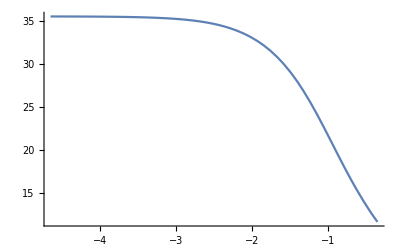

```mathematica
Module[{pemin,pemax,dp,TurnPoint,k,ExpInt,p,x,tabf},TurnPoint[e_?NumericQ]:=x/.FindRoot[e+1/x^6-αz x^2==0,{x,xi,xf}][[1]];(*Przybliżenie WKB*)
k[x_,e_]:=Sqrt[-(e+1/x^6-αz x^2)];
ExpInt[rf_?NumericQ,e_?NumericQ]:=NIntegrate[k[x,e],{x,TurnPoint[e],rf}];
pemin=Log[10,-emin];
pemax=Log[10,-emax];
tabf=Table[{p,x/.FindRoot[Exp[-ExpInt[x,-10^p]]==epsf,{x,TurnPoint[-10^p],xf}][[1]]},{p,pemin,pemax,(pemax-pemin)/nptf}];xfin=Interpolation[tabf];
Plot[xfin[x],{x,pemin,pemax}]]
```

Subroutine determining steps
Parameters:
npt -  number of points per one wave-lenght

InterpolatingFunction::dmval: Input value {0.100039} lies outside the range of data in the interpolating function. Extrapolation will be used.

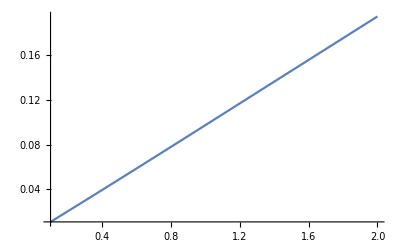

```mathematica
Module[{tab,eig,lambda,h,dbl,n},

tab=Table[eig=Eigenvalues[V[x]];{x,Min[Flatten[{2Pi/Sqrt[Abs[emin-eig]],2Pi/Sqrt[Abs[emax-eig]]}]]},{x,xi,xf,(xf-xi)/nptl}];
lambda=Interpolation[tab]; (*Local de Broglie wavelength (minimum over all channels). Used for determination of the step size *)

xt={};
h=lambda[xi]/npt;
AppendTo[xt,xi];
AppendTo[xt,xi+h];
dbl=1; (* dbl = 1 - step doubling or halving was done in the previous step, dbl = 0 otherwise *)
n=2;

While[(xt[[n]]<xf)||(dbl==1),
Which[
(lambda[xt[[n]]]≥2 npt h)&&(dbl==0),

h=2h;
AppendTo[xt,xt[[n]]+h];
dbl=1;,

(lambda[xt[[n]]]<npt h)&&(dbl==0),

h=h/2;
AppendTo[xt,xt[[n]]+h];
dbl=1;,

True,

AppendTo[xt,xt[[n]]+h];
dbl=0;
];
n++;
];
nstep=n;  (* Total number of steps *);
Plot[lambda[x],{x,0.1,2},PlotRange->All]
]
```

Number of steps

```mathematica
nstep
```

3894

Matching point (somewhere between xi and xf in the classically allowed regime). It position is determined versus position of the classical turning point for highest L

```mathematica
xmid=1
```

1

Location of the matching point in the table xt

```mathematica
nmid=1; 
While[xt[[nmid]]<xmid,nmid++];
nmid--
xt[[nmid]]
```

365

0.999683

Subroutine performing outward integration using renormalized Numerov method
It takes Psi0 as an initial condition

Parameters:
en - energy
n0 -  starting point (element of xt)
nf -  final point (element of xt)
phi - short-range phase
cl: if 1 clears table Rout (to save memory)

```mathematica
evolNumOut[en_?NumericQ,n0_?IntegerQ,nf_?IntegerQ,phi_?NumericQ,cl_?IntegerQ]:=
Module[{W,Qt,n,Rinv,h,h0,nodes,Ro},

nodes=0;

Rout[n0]=Psi0[xt[[n0+1]],phi].Inverse[Psi0[xt[[n0]],phi]];
nodes+=Length[Select[Eigenvalues[Rout[n0]],#<0&]];(*Which functions change sign*)
h=xt[[n0+1]]-xt[[n0]];
n=n0+1;

While[n<=nf,
h0=h;
h=xt[[n+1]]-xt[[n]];
Which[

Abs[h]>1.5 Abs[h0],
W=Id+(h^2/12) QT[[n+1]];
Rout[n]=Inverse[W].(2 Id -(5h^2/6)QT[[n]]-(Id+(h^2/12)QT[[n-2]]).Inverse[Rout[n-1].Rout[n-2]]);,

Abs[h]<0.75 Abs[h0],
Qt=(en + ref[[1]])Id-V[(xt[[n]]+xt[[n-1]])/2];
Rinv=Inverse[2 Id-(h0^2/12)Qt].((Id+(h0^2/12)QT[[n-1]]).Inverse[Rout[n-1]]+Id+(h0^2/12)QT[[n]]);
W=Id+(h^2/12) QT[[n+1]];
Rout[n]=Inverse[W].((2 Id -(5h^2/6)QT[[n]])-(Id+(h^2/12)Qt).Rinv);,

True,
W=Id+(h^2/12) QT[[n+1]];
Rout[n]=Inverse[W].((2 Id -(5h^2/6)QT[[n]])-(Id+(h^2/12)QT[[n-1]]).Inverse[Rout[n-1]]);
];
nodes+=Length[Select[Eigenvalues[Rout[n]],#<0&]];
n++;
];
Ro=Rout[nf];
Clear[W,Qt,n,Rinv,h,h0];
If[cl==1,Clear[Rout]];
{Ro,nodes}]
```

Subroutine performing inward integration using renormalized Noumerov method
It assumes that function vanishes at the starting value

Parameters:
Parameters:
en - energy
n0 -  starting point (element of xt)
nf -  final point (element of xt)
cl: if 1 clears table Rout (to save memory)

```mathematica
evolNumIn[en_?NumericQ,n0_?IntegerQ,nf_?IntegerQ,cl_?IntegerQ]:=
Module[{W,Qt,n,Rinv,h,h0,nodes,Ri},

nodes=0;
h=xt[[n0-2]]-xt[[n0-1]];
W=Id+(h^2/12) QT[[n0-2]];
Rin[n0-1]=Inverse[W].(2 Id -(5h^2/6)QT[[n0-1]]);
nodes+=Length[Select[Eigenvalues[Rin[n0-1]],#<0&]];
n=n0-2;

While[n>=nf,
h0=h;
h=xt[[n-1]]-xt[[n]];
Which[

Abs[h]>1.5 Abs[h0],
W=Id+(h^2/12) QT[[n-1]];
Rin[n]=Inverse[W].(2 Id -(5h^2/6)QT[[n]]-(Id+(h^2/12)QT[[n+2]]).Inverse[Rin[n+1].Rin[n+2]]);,

Abs[h]<0.75 Abs[h0],
Qt=(en+ref[[1]]) Id-V[(xt[[n]]+xt[[n+1]])/2];
Rinv=Inverse[2 Id-(h0^2/12)Qt].((Id+(h0^2/12)QT[[n+1]]).Inverse[Rin[n+1]]+Id+(h0^2/12)QT[[n]]);
W=Id+(h^2/12) QT[[n-1]];
Rin[n]=Inverse[W].((2 Id -(5h^2/6)QT[[n]])-(Id+(h^2/12)Qt).Rinv);,

True,
W=Id+(h^2/12) QT[[n-1]];
Rin[n]=Inverse[W].((2 Id -(5h^2/6)QT[[n]])-(Id+(h^2/12)QT[[n+1]]).Inverse[Rin[n+1]]);
];
nodes+=Length[Select[Eigenvalues[Rin[n]],#<0&]];
n--;
];
Ri=Rin[nf];
Clear[W,Qt,n,Rinv,h,h0];
If[cl==1,Clear[Rin]];
{Ri,nodes}]
```

Subroutine calculating determinant that should vanish at the matching point if the energy is correct

Parameters:
en -  energy
phi -  short range phase

```mathematica
EigenEn[en_?NumericQ,phi_?NumericQ]:=
Module[{n,win,wout,nodes,det,m,nmax},
QT=Table[(en+ref[[1]]) Id-V[xt[[n]]],{n,1,Length[xt]}];
nmax=nstep;
While[xt[[nmax]]>xfin[Log[10,-en]],nmax--];
win=evolNumIn[en,nmax,nmid+1,1]; (* Performs inward integration *)
wout=evolNumOut[en,1,nmid,phi,1];  (* Performs outward integration *)
nodes=win[[2]]+wout[[2]]; (* Total number of nodes *) 
m=wout[[1]]-Inverse[win[[1]]];
det=Det[m]; (*Calculates determinant that should vanish at the the matching point *)
Clear[n,win,wout,QT];
{det,nodes,m}
]
```

```mathematica
Timing[EigenEn[-3.,Pi/4]]
```

InterpolatingFunction::dmval: Input value {0.477121} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{0.5,{4.51947×10^-29,5,{{0.0158306,0.00267455,0.000769353,0.000058961,2.41307×10^-6,6.19653×10^-8,1.09195×10^-9,1.40155×10^-11,1.36785×10^-13,1.04879×10^-15,6.48214×10^-18,3.29725×10^-20,1.40422×10^-22,5.07948×10^-25,1.57988×10^-27,4.27003×10^-30,1.01213×10^-32,2.121×10^-35,3.95777×10^-38,6.61803×10^-41,9.97367×10^-44,1.36165×10^-46,1.69195×10^-49,1.92162×10^-52,2.00257×10^-55,1.92175×10^-58,1.70381×10^-61,1.39983×10^-64,1.06875×10^-67,7.60253×10^-71,5.05098×10^-74,3.14133×10^-77,1.8327×10^-80},{0.00267457,0.0169433,-0.00117655,-9.88142×10^-6,1.24566×10^-7,8.84842×10^-9,2.17884×10^-10,3.41226×10^-12,3.8527×10^-14,3.32411×10^-16,2.27265×10^-18,1.2637×10^-20,5.83104×10^-23,2.26931×10^-25,7.55007×10^-28,2.17215×10^-30,5.45746×10^-33,1.20776×10^-35,2.37217×10^-38,4.16287×10^-41,6.56635×10^-44,9.36003×10^-47,1.21162×10^-49,1.43058×10^-52,1.54692×10^-55,1.53758×10^-58,1.40961×10^-61,1.19568×10^-64,9.41123×10^-68,6.89228×10^-71,4.70819×10^-74,3.00703×10^-77,1.79954×10^-80},{0.000769362,-0.00117655,0.0253455,-0.000958913,-0.0000105108,-1.57438×10^-7,-2.14805×10^-9,-2.46424×10^-11,-2.32272×10^-13,-1.79466×10^-15,-1.14421×10^-17,-6.08082×10^-20,-2.72367×10^-22,-1.03943×10^-24,-3.41425×10^-27,-9.74303×10^-30,-2.43589×10^-32,-5.37653×10^-35,-1.05492×10^-37,-1.85149×10^-40,-2.92323×10^-43,-4.17331×10^-46,-5.41267×10^-49,-6.40502×10^-52,-6.94256×10^-55,-6.91804×10^-58,-6.35866×10^-61,-5.40769×10^-64,-4.26747×10^-67,-3.13331×10^-70,-2.14581×10^-73,-1.37388×10^-76,-8.24176×10^-80},{0.0000589622,-9.88123×10^-6,-0.000958914,0.036483,-0.000687922,-4.09091×10^-6,-3.40899×10^-8,-2.63213×10^-10,-1.74723×10^-12,-9.7682×10^-15,-4.57724×10^-17,-1.79852×10^-19,-5.93404×10^-22,-1.64305×10^-24,-3.79469×10^-27,-7.17369×10^-30,-1.05174×10^-32,-9.74877×10^-36,2.84691×10^-39,3.73912×10^-41,1.02368×10^-43,1.98962×10^-46,3.16941×10^-49,4.35338×10^-52,5.2873×10^-55,5.76416×10^-58,5.69835×10^-61,5.14664×10^-64,4.27167×10^-67,3.27373×10^-70,2.32598×10^-73,1.53743×10^-76,9.48275×10^-80},{2.41315×10^-6,1.24582×10^-7,-0.0000105108,-0.000687922,0.0475809,-0.00054122,-2.11311×10^-6,-1.22413×10^-8,-6.88756×10^-11,-3.48057×10^-13,-1.54477×10^-15,-5.98561×10^-18,-2.02539×10^-20,-6.00368×10^-23,-1.56596×10^-25,-3.61245×10^-28,-7.40924×10^-31,-1.35821×10^-33,-2.23657×10^-36,-3.32435×10^-39,-4.48033×10^-42,-5.49842×10^-45,-6.169×10^-48,-6.35105×10^-51,-6.02043×10^-54,-5.27176×10^-57,-4.27692×10^-60,-3.2238×10^-63,-2.26362×10^-66,-1.48423×10^-69,-9.10867×10^-73,-5.24328×10^-76,-2.83677×10^-79},{6.19683×10^-8,8.84911×10^-9,-1.57441×10^-7,-4.09092×10^-6,-0.000541221,0.0586877,-0.00044656,-1.23563×10^-6,-5.27251×10^-9,-2.2477×10^-11,-8.80862×10^-14,-3.09413×10^-16,-9.66269×10^-19,-2.67843×10^-21,-6.59862×10^-24,-1.44883×10^-26,-2.84512×10^-29,-5.01641×10^-32,-7.97343×10^-35,-1.14711×10^-37,-1.49961×10^-40,-1.78818×10^-43,-1.95194×10^-46,-1.95718×10^-49,-1.80844×10^-52,-1.54457×10^-55,-1.22288×10^-58,-8.99905×10^-62,-6.17083×10^-65,-3.95236×10^-68,-2.36976×10^-71,-1.33292×10^-74,-7.0472×10^-78},{1.09202×10^-9,2.17903×10^-10,-2.14813×10^-9,-3.40903×10^-8,-2.11312×10^-6,-0.00044656,0.069805,-0.00038025,-7.85862×10^-7,-2.58185×10^-9,-8.66637×10^-12,-2.72371×10^-14,-7.79552×10^-17,-2.01199×10^-19,-4.66892×10^-22,-9.74218×10^-25,-1.83082×10^-27,-3.10632×10^-30,-4.77211×10^-33,-6.65882×10^-36,-8.46651×10^-39,-9.84081×10^-42,-1.04894×10^-44,-1.02849×10^-47,-9.30373×10^-51,-7.7866×10^-54,-6.04557×10^-57,-4.36547×10^-60,-2.93885×10^-63,-1.8487×10^-66,-1.08902×10^-69,-6.01965×10^-73,-3.12834×10^-76},{1.40167×10^-11,3.41262×10^-12,-2.4644×10^-11,-2.63218×10^-10,-1.22414×10^-8,-1.23563×10^-6,-0.00038025,0.0809312,-0.000331157,-5.30928×10^-7,-1.38664×10^-9,-3.76824×10^-12,-9.7331×10^-15,-2.31921×10^-17,-5.04127×10^-20,-9.95653×10^-23,-1.78523×10^-25,-2.90835×10^-28,-4.31204×10^-31,-5.83094×10^-34,-7.20896×10^-37,-8.16976×10^-40,-8.50946×10^-43,-8.16779×10^-46,-7.24359×10^-49,-5.95058×10^-52,-4.53932×10^-55,-3.22316×10^-58,-2.13509×10^-61,-1.32232×10^-64,-7.67252×10^-68,-4.17905×10^-71,-2.14075×10^-74},{1.368×10^-13,3.85319×10^-14,-2.32293×10^-13,-1.74729×10^-12,-6.88769×10^-11,-5.27255×10^-9,-7.85863×10^-7,-0.000331157,0.0920646,-0.000293331,-3.75522×10^-7,-7.99069×10^-10,-1.79623×10^-12,-3.88633×10^-15,-7.84152×10^-18,-1.45734×10^-20,-2.48259×10^-23,-3.87057×10^-26,-5.52391×10^-29,-7.22413×10^-32,-8.67131×10^-35,-9.57135×10^-38,-9.73553×10^-41,-9.14531×10^-44,-7.95172×10^-47,-6.41388×10^-50,-4.80993×10^-53,-3.36089×10^-56,-2.1927×10^-59,-1.33842×10^-62,-7.65856×10^-66,-4.11577×10^-69,-2.08106×10^-72},{1.04893×10^-15,3.32462×10^-16,-1.79487×10^-15,-9.76866×10^-15,-3.48068×10^-13,-2.24774×10^-11,-2.58186×10^-9,-5.30929×10^-7,-0.000293331,0.103204,-0.00026329,-2.75366×10^-7,-4.86865×10^-10,-9.21047×10^-13,-1.69518×10^-15,-2.93668×10^-18,-4.7247×10^-21,-7.01989×10^-24,-9.61204×10^-27,-1.21252×10^-29,-1.40999×10^-32,-1.51321×10^-35,-1.50105×10^-38,-1.37859×10^-41,-1.17439×10^-44,-9.29717×10^-48,-6.85306×10^-51,-4.71247×10^-54,-3.02878×10^-57,-1.82284×10^-60,-1.02916×10^-63,-5.46048×10^-67,-2.72728×10^-70},{6.48316×10^-18,2.27307×10^-18,-1.14438×10^-17,-4.57752×10^-17,-1.54485×10^-15,-8.80887×10^-14,-8.66649×10^-12,-1.38665×10^-9,-3.75522×10^-7,-0.00026329,0.11435,-0.000238855,-2.07905×10^-7,-3.10389×10^-10,-5.01254×10^-13,-7.94877×10^-16,-1.19601×10^-18,-1.68328×10^-21,-2.20211×10^-24,-2.67092×10^-27,-3.0012×10^-30,-3.12499×10^-33,-3.01772×10^-36,-2.70576×10^-39,-2.25569×10^-42,-1.7511×10^-45,-1.26789×10^-48,-8.57652×10^-52,-5.42905×10^-55,-3.22141×10^-58,-1.79472×10^-61,-9.40335×10^-65,-4.64075×10^-68},{3.29787×10^-20,1.26397×10^-20,-6.08195×10^-20,-1.79865×10^-19,-5.98603×10^-18,-3.09427×10^-16,-2.72378×10^-14,-3.76828×10^-12,-7.99073×10^-10,-2.75366×10^-7,-0.000238855,0.1255,-0.00021859,-1.60804×10^-7,-2.05462×10^-10,-2.86658×10^-13,-3.95919×10^-16,-5.22526×10^-19,-6.49117×10^-22,-7.53847×10^-25,-8.1597×10^-28,-8.22275×10^-31,-7.71408×10^-34,-6.74072×10^-37,-5.49127×10^-40,-4.17512×10^-43,-2.96654×10^-46,-1.97246×10^-49,-1.22903×10^-52,-7.18708×10^-56,-3.95016×10^-59,-2.04357×10^-62,-9.96566×10^-66},{1.40453×10^-22,5.83249×10^-23,-2.72428×10^-22,-5.93453×10^-22,-2.02558×10^-20,-9.66331×10^-19,-7.79583×10^-17,-9.73332×10^-15,-1.79625×10^-12,-4.86867×10^-10,-2.07905×10^-7,-0.00021859,0.136656,-0.000201513,-1.2692×10^-7,-1.4039×10^-10,-1.70961×10^-13,-2.07573×10^-16,-2.42336×10^-19,-2.67796×10^-22,-2.78061×10^-25,-2.70362×10^-28,-2.45813×10^-31,-2.08917×10^-34,-1.66028×10^-37,-1.23457×10^-40,-8.59756×10^-44,-5.61331×10^-47,-3.43997×10^-50,-1.98117×10^-53,-1.07367×10^-56,-5.48247×10^-60,-2.6412×10^-63},{5.08075×10^-25,2.26995×10^-25,-1.0397×10^-24,-1.64319×10^-24,-6.0044×10^-23,-2.67866×10^-21,-2.01211×10^-19,-2.3193×10^-17,-3.88641×10^-15,-9.21056×10^-13,-3.1039×10^-10,-1.60804×10^-7,-0.000201514,0.147818,-0.000186928,-1.01922×10^-7,-9.8567×10^-11,-1.05699×10^-13,-1.13731×10^-16,-1.18327×10^-19,-1.17112×10^-22,-1.09408×10^-25,-9.61143×10^-29,-7.92661×10^-32,-6.13342×10^-35,-4.45319×10^-38,-3.03529×10^-41,-1.9436×10^-44,-1.17024×10^-47,-6.63197×10^-51,-3.54139×10^-54,-1.78385×10^-57,-8.48586×10^-61},{1.58033×10^-27,7.55251×10^-28,-3.41528×10^-27,-3.79494×10^-27,-1.56619×10^-25,-6.59936×10^-24,-4.6693×10^-22,-5.04155×10^-20,-7.84179×10^-18,-1.69522×10^-15,-5.01259×10^-13,-2.05463×10^-10,-1.2692×10^-7,-0.000186928,0.158985,-0.000174328,-8.30767×10^-8,-7.08492×10^-11,-6.74247×10^-14,-6.47496×10^-17,-6.0428×10^-20,-5.38899×10^-23,-4.55501×10^-26,-3.63426×10^-29,-2.73176×10^-32,-1.93302×10^-35,-1.28753×10^-38,-8.07494×10^-42,-4.77126×10^-45,-2.65804×10^-48,-1.39731×10^-51,-6.93805×10^-55,-3.25704×10^-58},{4.27141×10^-30,2.17294×10^-30,-9.74638×10^-30,-7.17379×10^-30,-3.61308×10^-28,-1.44903×10^-26,-9.7432×10^-25,-9.95728×10^-23,-1.45742×10^-20,-2.93677×10^-18,-7.94891×10^-16,-2.86661×10^-13,-1.4039×10^-10,-1.01922×10^-7,-0.000174328,0.170157,-0.000163333,-6.86015×10^-8,-5.19832×10^-11,-4.42045×10^-14,-3.81261×10^-17,-3.21022×10^-20,-2.59354×10^-23,-1.99336×10^-26,-1.45118×10^-29,-9.98528×10^-33,-6.48763×10^-36,-3.97914×10^-39,-2.30432×10^-42,-1.26049×10^-45,-6.51692×10^-49,-3.18693×10^-52,-1.4753×10^-55},{1.0125×10^-32,5.45967×10^-33,-2.43684×10^-32,-1.0516×10^-32,-7.41076×10^-31,-2.84559×10^-29,-1.83106×10^-27,-1.78541×10^-25,-2.48276×10^-23,-4.72493×10^-21,-1.19605×10^-18,-3.95926×10^-16,-1.70962×10^-13,-9.85674×10^-11,-8.30768×10^-8,-0.000163333,0.181335,-0.000153656,-5.72992×10^-8,-3.88385×10^-11,-2.96915×10^-14,-2.31292×10^-17,-1.7662×10^-20,-1.29892×10^-23,-9.11895×10^-27,-6.08304×10^-30,-3.84664×10^-33,-2.30323×10^-36,-1.30531×10^-39,-7.0022×10^-43,-3.55659×10^-46,-1.71132×10^-49,-7.80544×10^-53},{2.12186×10^-35,1.20831×10^-35,-5.37887×10^-35,-9.74163×10^-36,-1.35854×10^-33,-5.01739×10^-32,-3.10681×10^-30,-2.90871×10^-28,-3.87093×10^-26,-7.02035×10^-24,-1.68336×10^-21,-5.22541×10^-19,-2.07576×10^-16,-1.057×10^-13,-7.08494×10^-11,-6.86015×10^-8,-0.000153656,0.19252,-0.000145075,-4.8346×10^-8,-2.94888×10^-11,-2.03781×10^-14,-1.44096×10^-17,-1.0026×10^-20,-6.7415×10^-24,-4.34071×10^-27,-2.66342×10^-30,-1.55339×10^-33,-8.60058×10^-37,-4.51805×10^-40,-2.25174×10^-43,-1.06494×10^-46,-4.78128×10^-50},{3.95954×10^-38,2.37335×10^-38,-1.05543×10^-37,2.86917×10^-39,-2.23717×10^-36,-7.97524×10^-35,-4.77301×10^-33,-4.3127×10^-31,-5.52457×10^-29,-9.6129×10^-27,-2.20225×10^-24,-6.49145×10^-22,-2.42342×10^-19,-1.13732×10^-16,-6.74252×10^-14,-5.19834×10^-11,-5.72993×10^-8,-0.000145075,0.203711,-0.000137413,-4.1162×10^-8,-2.27149×10^-11,-1.4259×10^-14,-9.19422×10^-18,-5.85372×10^-21,-3.61298×10^-24,-2.14155×10^-27,-1.21291×10^-30,-6.54603×10^-34,-3.3617×10^-37,-1.64169×10^-40,-7.62243×10^-44,-3.36528×10^-47},{6.6213×10^-41,4.16515×10^-41,-1.85248×10^-40,3.74456×10^-41,-3.32536×10^-39,-1.14741×10^-37,-6.66028×10^-36,-5.832×10^-34,-7.22519×10^-32,-1.21266×10^-29,-2.67114×10^-27,-7.53892×10^-25,-2.67806×10^-22,-1.1833×10^-19,-6.47505×10^-17,-4.42048×10^-14,-3.88387×10^-11,-4.83461×10^-8,-0.000137413,0.214908,-0.000130532,-3.53309×10^-8,-1.77254×10^-11,-1.01528×10^-14,-5.99437×10^-18,-3.50572×10^-21,-1.99338×10^-24,-1.09142×10^-27,-5.72405×10^-31,-2.86731×10^-34,-1.36971×10^-37,-6.23494×10^-41,-2.70378×10^-44},{9.97908×10^-44,6.57028×10^-44,-2.92495×10^-43,1.02479×10^-43,-4.48186×10^-42,-1.50005×10^-40,-8.46864×10^-39,-7.21049×10^-37,-8.67283×10^-35,-1.41018×10^-32,-3.00152×10^-30,-8.16035×10^-28,-2.78077×10^-25,-1.17117×10^-22,-6.04294×10^-20,-3.81266×10^-17,-2.96917×10^-14,-2.94889×10^-11,-4.1162×10^-8,-0.000130532,0.226112,-0.000124317,-3.05487×10^-8,-1.39951×10^-11,-7.34411×10^-15,-3.98539×10^-18,-2.1486×10^-21,-1.12924×10^-24,-5.72906×10^-28,-2.79057×10^-31,-1.30105×10^-34,-5.79649×10^-38,-2.46563×10^-41},{1.36246×10^-46,9.36613×10^-47,-4.17599×10^-46,1.99158×10^-46,-5.50052×10^-45,-1.78877×10^-43,-9.84362×10^-42,-8.17176×10^-40,-9.57332×10^-38,-1.51347×10^-35,-3.12542×10^-33,-8.2236×10^-31,-2.70383×10^-28,-1.09414×10^-25,-5.38918×10^-23,-3.2103×10^-20,-2.31295×10^-17,-2.03782×10^-14,-2.27149×10^-11,-3.53309×10^-8,-0.000124317,0.237324,-0.000118678,-2.65898×10^-8,-1.11683×10^-11,-5.38937×10^-15,-2.69741×10^-18,-1.34491×10^-21,-6.55345×10^-25,-3.08968×10^-28,-1.40153×10^-31,-6.0976×10^-35,-2.53985×10^-38},{1.69305×10^-49,1.21248×10^-49,-5.41645×10^-49,3.17246×10^-49,-6.17161×10^-48,-1.95266×10^-46,-1.04928×10^-44,-8.51183×10^-43,-9.73785×10^-41,-1.50135×10^-38,-3.01821×10^-36,-7.71508×10^-34,-2.45837×10^-31,-9.61213×10^-29,-4.55524×10^-26,-2.59363×10^-23,-1.76624×10^-20,-1.44098×10^-17,-1.42591×10^-14,-1.77254×10^-11,-3.05487×10^-8,-0.000118679,0.248543,-0.000113539,-2.32845×10^-8,-8.99975×10^-12,-4.00727×10^-15,-1.85575×10^-18,-8.5827×10^-22,-3.8884×10^-25,-1.70813×10^-28,-7.23414×10^-32,-2.944×10^-35},{1.92297×10^-52,1.43168×10^-52,-6.40987×10^-52,4.3576×10^-52,-6.35401×10^-51,-1.95797×10^-49,-1.02886×10^-47,-8.17035×10^-46,-9.14779×10^-44,-1.37891×10^-41,-2.70628×10^-39,-6.74179×10^-37,-2.08943×10^-34,-7.92737×10^-32,-3.63451×10^-29,-1.99346×10^-26,-1.29897×10^-23,-1.00262×10^-20,-9.19433×10^-18,-1.01528×10^-14,-1.39951×10^-11,-2.65898×10^-8,-0.000113539,0.25977,-0.000108836,-2.05033×10^-8,-7.3173×10^-12,-3.01579×10^-15,-1.29601×10^-18,-5.57541×10^-22,-2.35467×10^-25,-9.66186×10^-29,-3.82934×10^-32},{2.00409×10^-55,1.5482×10^-55,-6.94824×10^-55,5.29258×10^-55,-6.0235×10^-54,-1.80925×10^-52,-9.30742×10^-51,-7.24613×10^-49,-7.95416×10^-47,-1.1747×10^-44,-2.2562×10^-42,-5.4923×10^-40,-1.66053×10^-37,-6.13416×10^-35,-2.73201×10^-32,-1.45128×10^-29,-9.11938×10^-27,-6.74172×10^-24,-5.85384×10^-21,-5.99444×10^-18,-7.34415×10^-15,-1.11683×10^-11,-2.32845×10^-8,-0.000108836,0.271006,-0.000104516,-1.81464×10^-8,-5.99846×10^-12,-2.295×10^-15,-9.17727×10^-19,-3.68178×10^-22,-1.45302×10^-25,-5.58192×10^-29},{1.92333×10^-58,1.53895×10^-58,-6.92414×10^-58,5.77013×10^-58,-5.2747×10^-57,-1.54533×10^-55,-7.79×10^-54,-5.95289×10^-52,-6.41608×10^-50,-9.29996×10^-48,-1.75156×10^-45,-4.17604×10^-43,-1.2348×10^-40,-4.45385×10^-38,-1.93325×10^-35,-9.98616×10^-33,-6.08344×10^-30,-4.34091×10^-27,-3.61309×10^-24,-3.50579×10^-21,-3.98544×10^-18,-5.38941×10^-15,-8.99977×10^-12,-2.05033×10^-8,-0.000104516,0.28225,-0.000100534,-1.61359×10^-8,-4.95476×10^-12,-1.76453×10^-15,-6.58235×10^-19,-2.46854×10^-22,-9.12425×10^-26},{1.70531×10^-61,1.41096×10^-61,-6.36468×10^-61,5.70452×10^-61,-4.27952×10^-60,-1.22354×10^-58,-6.04846×10^-57,-4.54127×10^-55,-4.81176×10^-53,-6.85537×10^-51,-1.26827×10^-48,-2.96729×10^-46,-8.5994×10^-44,-3.03583×10^-41,-1.28771×10^-38,-6.48836×10^-36,-3.84697×10^-33,-2.66359×10^-30,-2.14165×10^-27,-1.99344×10^-24,-2.14864×10^-21,-2.69744×10^-18,-4.00729×10^-15,-7.31732×10^-12,-1.81464×10^-8,-0.000100534,0.293502,-0.0000968538,-1.44105×10^-8,-4.12151×10^-12,-1.36967×10^-15,-4.77761×10^-19,-1.67862×10^-22},{1.40115×10^-64,1.1969×10^-64,-5.41318×10^-64,5.15248×10^-64,-3.22593×10^-63,-9.00429×10^-62,-4.36775×10^-60,-3.22467×10^-58,-3.3623×10^-56,-4.71423×10^-54,-8.57935×10^-52,-1.97303×10^-49,-5.61469×10^-47,-1.944×10^-44,-8.07633×10^-42,-3.97969×10^-39,-2.30348×10^-36,-1.55352×10^-33,-1.21298×10^-30,-1.09146×10^-27,-1.12928×10^-24,-1.34493×10^-21,-1.85577×10^-18,-3.01581×10^-15,-5.99848×10^-12,-1.61359×10^-8,-0.0000968538,0.304764,-0.0000934414,-1.29214×10^-8,-3.45082×10^-12,-1.07262×10^-15,-3.50627×10^-19},{1.06983×10^-67,9.42149×10^-68,-4.2721×10^-67,4.27676×10^-67,-2.26524×10^-66,-6.17473×10^-65,-2.94051×10^-63,-2.13618×10^-61,-2.19371×10^-59,-3.03003×10^-57,-5.43104×10^-55,-1.22943×10^-52,-3.44094×10^-50,-1.17052×10^-47,-4.77223×10^-45,-2.30471×10^-42,-1.30549×10^-39,-8.60148×10^-37,-6.54656×10^-34,-5.72439×10^-31,-5.7293×10^-28,-6.55363×10^-25,-8.58285×10^-22,-1.29603×10^-18,-2.29502×10^-15,-4.95477×10^-12,-1.44105×10^-8,-0.0000934415,0.316036,-0.0000902693,-1.16295×10^-8,-2.90688×10^-12,-8.46964×10^-16},{7.61076×10^-71,6.90029×10^-71,-3.13693×10^-70,3.27784×10^-70,-1.48537×10^-69,-3.95505×10^-68,-1.84983×10^-66,-1.32305×10^-64,-1.3391×10^-62,-1.82367×10^-60,-3.22272×10^-58,-7.18968×10^-56,-1.9818×10^-53,-6.6338×10^-51,-2.65866×10^-48,-1.26074×10^-45,-7.00333×10^-43,-4.51864×10^-40,-3.36205×10^-37,-2.86753×10^-34,-2.79073×10^-31,-3.08981×10^-28,-3.88851×10^-25,-5.5755×10^-22,-9.17736×10^-19,-1.76454×10^-15,-4.12152×10^-12,-1.29214×10^-8,-0.0000902693,0.327317,-0.0000873131,-1.05033×10^-8,-2.46259×10^-12},{5.05681×10^-74,4.71401×10^-74,-2.14845×10^-73,2.32905×10^-73,-9.11621×10^-73,-2.37151×10^-71,-1.08974×10^-69,-7.67714×10^-68,-7.66275×10^-66,-1.02967×10^-63,-1.79553×10^-61,-3.95174×10^-59,-1.07406×10^-56,-3.5425×10^-54,-1.39769×10^-51,-6.51842×10^-49,-3.55727×10^-46,-2.2521×10^-43,-1.6419×10^-40,-1.36984×10^-37,-1.30115×10^-34,-1.40161×10^-31,-1.7082×10^-28,-2.35473×10^-25,-3.68184×10^-22,-6.58241×10^-19,-1.36967×10^-15,-3.45083×10^-12,-1.16295×10^-8,-0.0000873131,0.338609,-0.0000845518,-9.51701×10^-9},{3.14519×10^-77,3.01097×10^-77,-1.37568×10^-76,1.53956×10^-76,-5.24793×10^-76,-1.33397×10^-74,-6.02395×10^-73,-4.18177×10^-71,-4.11821×10^-69,-5.46341×10^-67,-9.40793×10^-65,-2.04447×10^-62,-5.48463×10^-60,-1.78447×10^-57,-6.94017×10^-55,-3.18777×10^-52,-1.7117×10^-49,-1.06514×10^-46,-7.62361×10^-44,-6.23571×10^-41,-5.79705×10^-38,-6.09804×10^-35,-7.23452×10^-32,-9.66222×10^-29,-1.45306×10^-25,-2.46858×10^-22,-4.77766×10^-19,-1.07263×10^-15,-2.90688×10^-12,-1.05033×10^-8,-0.0000845519,0.349911,-0.0000819671},{1.83509×10^-80,1.80204×10^-80,-8.25318×10^-80,9.49659×10^-80,-2.83946×10^-79,-7.05316×10^-78,-3.13074×10^-76,-2.14225×10^-74,-2.08239×10^-72,-2.72887×10^-70,-4.64321×10^-68,-9.97046×10^-66,-2.64234×10^-63,-8.48914×10^-61,-3.25815×10^-58,-1.47575×10^-55,-7.80746×10^-53,-4.78233×10^-50,-3.3659×10^-47,-2.70418×10^-44,-2.46592×10^-41,-2.54008×10^-38,-2.94421×10^-35,-3.82953×10^-32,-5.58213×10^-29,-9.12448×10^-26,-1.67865×10^-22,-3.5063×10^-19,-8.46969×10^-16,-2.4626×10^-12,-9.51702×10^-9,-0.0000819671,0.361224}}}}

```mathematica
detphi[ph_?NumericQ,en_?NumericQ]:=Module[{wout,m,det},
wout=evolNumOut[en,1,nmid,ph,1];
m=wout[[1]]-Inverse[win[[1]]];
det=Det[m]; (*Calculates determinant that should vanish at the the matching point *)
Clear[wout];
{det,m}]
```

Subroutine determining roots with the renormalized Noumerov method

Parameters:
en - energy of bound state
nst - 

Output:
tabsol -  table containing eigenenergies
tabm -  table of corresponding matrices that are used to dermine eigenvectors (null space vectors)

```mathematica
RootsF[en_?NumericQ,nst_?NumericQ]:=
Module[{nmax,tab,phi,n,xn,fn,tabR,tabsol,tabm,fun,x,tabv},
QT=Table[(en+ref[[1]]) Id-V[xt[[n]]],{n,1,Length[xt]}];
nmax=nstep;
While[xt[[nmax]]>xfin[Log[10,-en]],nmax--];
win=evolNumIn[en,nmax,nmid+1,1]; (* Performs inward integration *)
tab=Table[{phi,detphi[phi,en]},{phi,phimin,phimax,Pi/nst}];
tabR={};
fun[x_?NumericQ]:=detphi[x,en][[1]];
For[n=1,n<Length[tab],n++,
If[(tab[[n,2,1]]tab[[n+1,2,1]]<=0),
xn=(tab[[n+1,1]]+tab[[n,1]])/2;
fn=fun[xn];
If[(tab[[n,2,1]]-fn)(tab[[n+1,2,1]]-fn)<0,AppendTo[tabR,{tab[[n,1]],tab[[n+1,1]]}]];
]
];
tabsol=Table[x/.FindRoot[fun[x]==0,{x,tabR[[n,1]],tabR[[n,2]]},Method->"Brent",PrecisionGoal->9][[1]],{n,1,Length[tabR]}];
tabm=Table[detphi[tabsol[[n]],en][[2]],{n,1,Length[tabsol]}];
tabv=Table[NullSpace[tabm[[n]],Tolerance->10^-4][[1]],{n,1,Length[tabm]}];
Clear[tab,nmax,phi,n,xn,fn,tabR,fun,x,QT];
(*Print["tabsol=",tabsol]*);
{tabsol,tabv}]
```

```mathematica
RootsFOld[phi_?NumericQ,emn_?NumericQ,emx_?NumericQ]:=
Module[{tab,tabnew,tabR,pemin,pemax,dp=0.005,fun,tabsol,x,tabm,tabv},
pemin=Log[10,-emn];
pemax=Log[10,-emx];
tabnew=Table[{pen,EigenEn[-10^pen,phi]},{pen,pemin,pemax,dp}];
tabR={};
fun[x_?NumericQ]:=EigenEn[-10^x,phi][[1]];
Do[If[(tabnew[[n,2,1]]tabnew[[n+1,2,1]]<0)&&(tabnew[[n,2,2]]==tabnew[[n+1,2,2]]),AppendTo[tabR,{tabnew[[n,1]],tabnew[[n+1,1]]}]],{n,1,Length[tabnew]-1}];
tab=Table[{tabnew[[n,1]],tabnew[[n,2,1]]},{n,1,Length[tabnew]}];
tabsol=Table[x/.FindRoot[fun[x]==0,{x,tabR[[n,1]],tabR[[n,2]]},Method->"Brent"][[1]],{n,1,Length[tabR]}];
tabm=Table[EigenEn[-10^tabsol[[n]],phi][[3]],{n,1,Length[tabsol]}];
{tabsol,tabm}]
```

```mathematica
ash[phi_]:=(Pi/8)(1+Tan[phi])/Gamma[5/4]^2
ϕ[a_]:=ArcTan[-((8*Gamma[5/4]^2)/π a-1)];
```

Subroutine calculating the wave function at the grid points in xt

Parameters:
phi - short-range phase
vec -  corerespondin eigenvector (value of the wave function at the matching point)

```mathematica
CalcPsi[phi_?NumericQ,en_?NumericQ,vecp_]:=Module[{win,wout,n,pe,nmax},
pe=Log[10,-en];
QT=Table[(en+ref[[1]]) Id-V[xt[[n]]],{n,1,Length[xt]}];
nmax=nstep;
While[xt[[nmax]]>xfin[pe],nmax--];
win=evolNumIn[en,nmax,nmid+1,0]; (* Performs inward integration *)
wout=evolNumOut[en,1,nmid,phi,0];  (* Performs outward integration *)
Psi[nmid]=vecp;
Do[Psi[n]=Inverse[Rout[n]].Psi[n+1],{n,nmid-1,1,-1}];
Do[Psi[n]=Inverse[Rin[n]].Psi[n-1],{n,nmid+1,nmax-1}];
Psi[nmax]=0 Id.Psi[nmax-1];
Do[Psi[n]=0 Id.Psi[n-1];,{n,nmax+1,nstep}];
]
```

```mathematica
RootsF[-1,50];//AbsoluteTiming
```

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{9.41258,Null}

```mathematica
rts={};
dp=0.1;

Module[{pemin,pemax,pen,tabp,p},
pemin=Log[10,-emin];
pemax=Log[10,-emax];
tabp={};
p=pemin;
While[p≤pemax,AppendTo[tabp,p];p+=dp];
Print[tabp];
Print["Progress:"];
Print[ProgressIndicator[Dynamic[n],{1,Length[tabp]}]];
xf = 100;

Do[en=-10^tabp[[i]];
n=i;
nmid=1; 
While[xt[[nmid]]<xmid,nmid++];
nmid--;

(*Print["xi = ",xi, " xf = ",xf," xmid = ", xmid];*)


AppendTo[rts,{-10^tabp[[i]],RootsF[-10^tabp[[i]],50]}];

,{i,1,Length[tabp]}
]
]
```

{-4.65667,-4.55667,-4.45667,-4.35667,-4.25667,-4.15667,-4.05667,-3.95667,-3.85667,-3.75667,-3.65667,-3.55667,-3.45667,-3.35667,-3.25667,-3.15667,-3.05667,-2.95667,-2.85667,-2.75667,-2.65667,-2.55667,-2.45667,-2.35667,-2.25667,-2.15667,-2.05667,-1.95667,-1.85667,-1.75667,-1.65667,-1.55667,-1.45667,-1.35667,-1.25667,-1.15667,-1.05667,-0.956666,-0.856666,-0.756666,-0.656666,-0.556666,-0.456666,-0.356666}

Progress:

```mathematica
taben={};tabphi={};tabvec={};
Do[AppendTo[taben,{aHOz/ash[rts[[n,2,1,m]]],1/Ωz rts[[n,1]]}];AppendTo[tabphi,{rts[[n,2,1,m]],rts[[n,1]]}];AppendTo[tabvec,rts[[n,2,2,m]]],{n,1,Length[rts]},{m,1,Length[rts[[n,2,1]]]}];
```

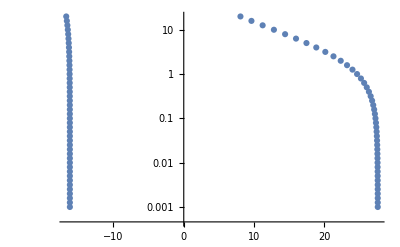

{{-27.6055,-0.001},{16.2036,-0.001},{-27.6046,-0.00125893},{16.2036,-0.00125893},{-27.6035,-0.00158489},{16.2036,-0.00158489},{-27.6021,-0.00199526},{16.2036,-0.00199526},{-27.6004,-0.00251189},{16.2036,-0.00251189},{-27.5982,-0.00316228},{16.2037,-0.00316228},{-27.5955,-0.00398107},{16.2037,-0.00398107},{-27.5921,-0.00501187},{16.2037,-0.00501187},{-27.5877,-0.00630957},{16.2038,-0.00630957},{-27.5823,-0.00794328},{16.2038,-0.00794328},{-27.5755,-0.01},{16.2039,-0.01},{-27.5668,-0.0125893},{16.204,-0.0125893},{-27.556,-0.0158489},{16.2041,-0.0158489},{-27.5424,-0.0199526},{16.2043,-0.0199526},{-27.5252,-0.0251189},{16.2045,-0.0251189},{-27.5037,-0.0316228},{16.2047,-0.0316228},{-27.4766,-0.0398107},{16.205,-0.0398107},{-27.4426,-0.0501187},{16.2054,-0.0501187},{-27.3999,-0.0630957},{16.2059,-0.0630957},{-27.3464,-0.0794328},{16.2065,-0.0794328},{-27.2793,-0.1},{16.2072,-0.1},{-27.1954,-0.125893},{16.2082,-0.125893},{-27.0906,-0.158489},{16.2094,-0.158489},{-26.9599,-0.199526},{16.2109,-0.199526},{-26.7973,-0.251189},{16.2127,-0.251189},{-26.5956,-0.316228},{16.2151,-0.316228},{-26.3465,-0.398107},{16.218,-0.398107},{-26.04,-0.501187},{16.2217,-0.501187},{-25.6652,-0.630957},{16.2263,-0.630957},{-25.2098,-0.794328},{16.2321,-0.794328},{-24.6611,-1.},{16.2392,-1.},{-24.0063,-1.25893},{16.2481,-1.25893},{-23.2339,-1.58489},{16.2591,-1.58489},{-22.3349,-1.99526},{16.2726,-1.99526},{-21.3041,-2.51189},{16.2892,-2.51189},{-20.1421,-3.16228},{16.3095,-3.16228},{-18.8557,-3.98107},{16.3342,-3.98107},{-17.4591,-5.01187},{16.3642,-5.01187},{-15.9721,-6.30957},{16.4004,-6.30957},{-14.4195,-7.94328},{16.4439,-7.94328},{-12.8281,-10.},{16.4962,-10.},{-11.2241,-12.5893},{16.5587,-12.5893},{-9.63084,-15.8489},{16.6334,-15.8489},{-8.06762,-19.9526},{16.7229,-19.9526}}

```mathematica
ListLogPlot[-taben,PlotRange->All]
taben
```

```mathematica
emin = -emin; emax = -emax;
```

```mathematica
rts1={};
Module[{pemin,pemax,pen,tabe,p},
tabe={};
dp=0.0008 emax;
p=emin;
While[p≤emax,AppendTo[tabe,p];p+=dp];
(*Print[tabe];*)
Print["Progress:"];
Print[ProgressIndicator[Dynamic[k],{1,Length[tabe]}]];
xf = 100;
Do[en=tabe[[i]];
(*Print["en = ",en];*)
k=i;
nmid=1; 
While[xt[[nmid]]<xmid,nmid++];
nmid--;

(*Print["xi = ",xi, " xf = ",xf," xmid = ", xmid];*)


AppendTo[rts1, {tabe[[i]],RootsF[tabe[[i]],50]}]

,{i,1,Length[tabe]}
]
]
```

Progress:

```mathematica
taben1={};tabphi1={};tabvec1={};
Do[AppendTo[taben1,{aHOz/ash[rts1[[n,2,1,m]]],1/Ωz rts1[[n,1]]}];AppendTo[tabphi1,{rts1[[n,2,1,m]],rts1[[n,1]]}];AppendTo[tabvec1,rts1[[n,2,2,m]]],{n,1,Length[rts1]},{m,1,Length[rts1[[n,2,1]]]}];
```

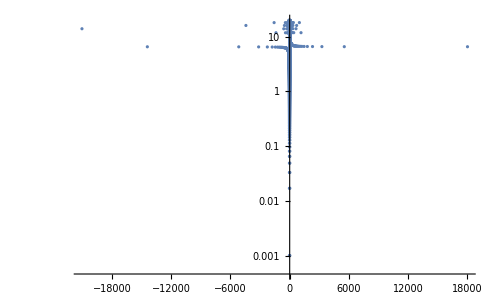

{{-27.6055,-0.001},{16.2036,-0.001},{-27.6046,-0.00125893},{16.2036,-0.00125893},{-27.6035,-0.00158489},{16.2036,-0.00158489},{-27.6021,-0.00199526},{16.2036,-0.00199526},{-27.6004,-0.00251189},{16.2036,-0.00251189},{-27.5982,-0.00316228},{16.2037,-0.00316228},{-27.5955,-0.00398107},{16.2037,-0.00398107},{-27.5921,-0.00501187},{16.2037,-0.00501187},{-27.5877,-0.00630957},{16.2038,-0.00630957},{-27.5823,-0.00794328},{16.2038,-0.00794328},{-27.5755,-0.01},{16.2039,-0.01},{-27.5668,-0.0125893},{16.204,-0.0125893},{-27.556,-0.0158489},{16.2041,-0.0158489},{-27.5424,-0.0199526},{16.2043,-0.0199526},{-27.5252,-0.0251189},{16.2045,-0.0251189},{-27.5037,-0.0316228},{16.2047,-0.0316228},{-27.4766,-0.0398107},{16.205,-0.0398107},{-27.4426,-0.0501187},{16.2054,-0.0501187},{-27.3999,-0.0630957},{16.2059,-0.0630957},{-27.3464,-0.0794328},{16.2065,-0.0794328},{-27.2793,-0.1},{16.2072,-0.1},{-27.1954,-0.125893},{16.2082,-0.125893},{-27.0906,-0.158489},{16.2094,-0.158489},{-26.9599,-0.199526},{16.2109,-0.199526},{-26.7973,-0.251189},{16.2127,-0.251189},{-26.5956,-0.316228},{16.2151,-0.316228},{-26.3465,-0.398107},{16.218,-0.398107},{-26.04,-0.501187},{16.2217,-0.501187},{-25.6652,-0.630957},{16.2263,-0.630957},{-25.2098,-0.794328},{16.2321,-0.794328},{-24.6611,-1.},{16.2392,-1.},{-24.0063,-1.25893},{16.2481,-1.25893},{-23.2339,-1.58489},{16.2591,-1.58489},{-22.3349,-1.99526},{16.2726,-1.99526},{-21.3041,-2.51189},{16.2892,-2.51189},{-20.1421,-3.16228},{16.3095,-3.16228},{-18.8557,-3.98107},{16.3342,-3.98107},{-17.4591,-5.01187},{16.3642,-5.01187},{-15.9721,-6.30957},{16.4004,-6.30957},{-14.4195,-7.94328},{16.4439,-7.94328},{-12.8281,-10.},{16.4962,-10.},{-11.2241,-12.5893},{16.5587,-12.5893},{-9.63084,-15.8489},{16.6334,-15.8489},{-8.06762,-19.9526},{16.7229,-19.9526}}

```mathematica
ListLogPlot[taben1,PlotRange->All]
taben
```

```mathematica
{1,1}
```

{1,1}

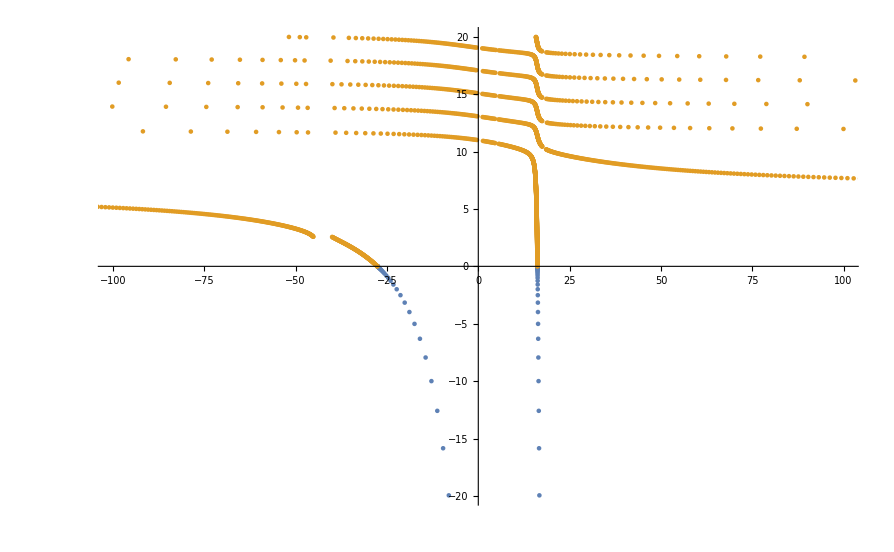

```mathematica
ListPlot[{taben,taben1},PlotRange->{{-100,100},{-20,20}}]
```

```mathematica
Export["Drop_3D_30_07.csv",Join[taben,taben1]]
```

Drop_3D_30_07.csv

```mathematica
tabb=Join[taben,taben1];
```

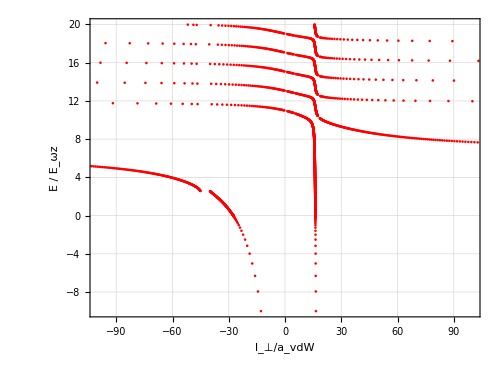

```mathematica
ListPlot[tabb,PlotRange->{{-100,100},{-10,20}},
AspectRatio->0.75,
Frame->True, FrameStyle->{{Directive[Thickness[0.005],Black],Directive[Thickness[0.005],Black]},{Directive[Thickness[0.005],Black],Directive[Thickness[0.005],Black]}},
PlotStyle->{Thick,{Red,Dashed}},FrameLabel->{Style["l_⊥/a_vdW",FontSize->20, FontFamily->"Times New Roman",FontWeight->Bold],Style["E / E_ωz",FontSize->20,FontWeight->Bold, FontFamily->"Times"]},GridLines->Automatic, GridLinesStyle->Directive[Thin, Dashed, LightGray],ImagePadding->50,ImageSize->500]
```

```mathematica
new=FindCurvePath[tabb.{{1,0},{0,100}}];
new1=Join[tabb[[#]]&/@new];
```

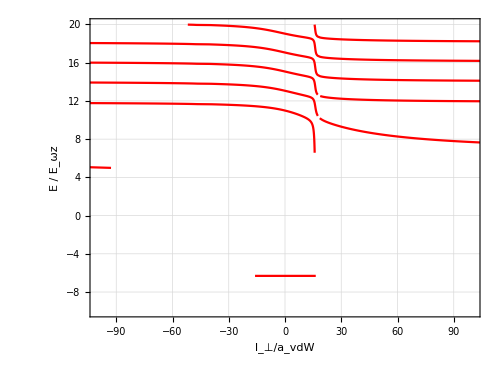

```mathematica
ListLinePlot[new1,PlotRange->{{-100,100},{-10,20}},
AspectRatio->0.75,
Frame->True, FrameStyle->{{Directive[Thickness[0.005],Black],Directive[Thickness[0.005],Black]},{Directive[Thickness[0.005],Black],Directive[Thickness[0.005],Black]}},
PlotStyle->Red,FrameLabel->{Style["l_⊥/a_vdW",FontSize->20, FontFamily->"Times New Roman",FontWeight->Bold],Style["E / E_ωz",FontSize->20,FontWeight->Bold, FontFamily->"Times"]},GridLines->Automatic, GridLinesStyle->Directive[Thin, Dashed, LightGray],ImagePadding->50,ImageSize->500]
```

```mathematica
tabela=Import["Drop_3D_30_07_2.csv"]
```

Import::nffil: File Drop_3D_30_07_2.csv not found during Import.

$Failed